```mathematica
3*5-2*7
```

1

```mathematica
Det[{{2,5,3},{7,11,13},{23,19,17}}]
```

420

```mathematica
9!
```

362880

```mathematica
Partition[Range[9],3]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
ps=Partition[#,3]&/@Permutations[Prime/@Range[9]];
```

```mathematica
ds=Det/@ps;
```

```mathematica
Length@ds
```

362880

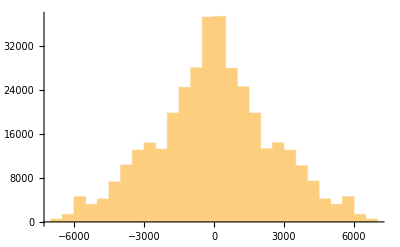

```mathematica
Histogram[ds]
```

```mathematica
sds=Sort[ds,Abs[#1]>Abs[#2]&];
```

```mathematica
Sort[Abs[ds]]//DeleteDuplicates//Differences//Sort//DeleteDuplicates
```

{2,4,6,8,10,12,14,16,18,20,22,24,28,30,34,38,52,62}

```mathematica
Position[ds,0]//Flatten
```

```mathematica
ps[[%]]
```

```mathematica
winners=%303;
```

```mathematica
MatrixForm/@%
```

```mathematica
Length@winners
```

216

```mathematica
216/(3! 3!)
```

6

```mathematica
?GatherBy
```

GatherBy[list,f] gathers into sublists each set of elements in list that gives the same value when f is applied.
GatherBy[list,{f_1,f_2,…}] gathers list into nested sublists using f_i at level i.

```mathematica
GatherBy[winners,Transpose[Sort@Transpose[Sort@#]]&];
```

```mathematica
DeleteDuplicates[Transpose[Sort@Transpose[Sort@#]]&/@winners]
```

{{{2,3,5},{13,11,7},{17,19,23}},{{2,5,19},{7,13,23},{11,17,3}},{{2,7,11},{5,13,17},{19,23,3}},{{2,7,11},{13,17,5},{19,23,3}},{{2,13,17},{3,11,19},{5,7,23}},{{2,13,19},{7,17,23},{11,5,3}},{{3,5,11},{19,13,2},{23,17,7}},{{3,11,17},{19,2,5},{23,7,13}},{{3,19,23},{5,13,17},{11,2,7}},{{3,19,23},{11,2,7},{17,5,13}},{{5,7,23},{3,11,19},{2,13,17}}}

```mathematica
%//Length
```

11

```mathematica
MatrixForm/@%323
```

{(2 | 3 | 5
13 | 11 | 7
17 | 19 | 23),(2 | 5 | 19
7 | 13 | 23
11 | 17 | 3),(2 | 7 | 11
5 | 13 | 17
19 | 23 | 3),(2 | 7 | 11
13 | 17 | 5
19 | 23 | 3),(2 | 13 | 17
3 | 11 | 19
5 | 7 | 23),(2 | 13 | 19
7 | 17 | 23
11 | 5 | 3),(3 | 5 | 11
19 | 13 | 2
23 | 17 | 7),(3 | 11 | 17
19 | 2 | 5
23 | 7 | 13),(3 | 19 | 23
5 | 13 | 17
11 | 2 | 7),(3 | 19 | 23
11 | 2 | 7
17 | 5 | 13),(5 | 7 | 23
3 | 11 | 19
2 | 13 | 17)}

{2,3,5,7,11,13,17,19,23,29}

```mathematica
winners[[3]]//MatrixForm
```

(2 | 5 | 3
13 | 7 | 11
17 | 23 | 19)

```mathematica
Transpose[Sort@Transpose[Sort@winners[[3]]]]//MatrixForm
```

(2 | 3 | 5
13 | 11 | 7
17 | 19 | 23)

```mathematica
Prime/@Range[10]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
ps2=Partition[#,3]&/@Permutations[{2,3,5,7,11,13,17,19,29}];
```

```mathematica
ds2=Det/@ps2;
```

```mathematica
Sort[Abs[ds2]]//DeleteDuplicates
```

```mathematica
Det[{{21,8,6},{1,2,3},{4,5,7}}]
```

1

```mathematica
m={{12,8,9},{1,2,3},{4,5,7}}
```

{{12,8,9},{1,2,3},{4,5,7}}

```mathematica
MatrixForm@Transpose@Sort@Transpose@Sort@m
```

(1 | 2 | 3
4 | 5 | 7
12 | 8 | 9)

```mathematica
Det[{{3,2},{7,5}}]
```

1

```mathematica
ps3=Partition[#,3]&/@Permutations[Range[9]];
```

```mathematica
ds3=Det/@ps3;
```

```mathematica
DeleteDuplicates[Sort[Abs[ds3]]][[;;10]]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
Sort[(Transpose@Sort@Transpose@Sort@#)&/@ps3[[Position[ds3,1]//Flatten]]]
```

{{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{7,5,8}},{{1,2,3},{4,6,9},{8,5,7}},{{1,2,3},{4,6,9},{8,5,7}},{{1,2,3},{4,6,9},{8,5,7}},{{1,2,3},{4,6,9},{8,5,7}},1132,{{4,7,8},{6,1,3},{9,2,5}},{{4,7,8},{6,1,3},{9,2,5}},{{4,7,8},{6,1,3},{9,2,5}},{{4,7,8},{6,1,3},{9,2,5}},{{5,6,8},{2,7,4},{1,9,3}},{{5,6,8},{2,7,4},{1,9,3}},{{5,6,8},{2,7,4},{1,9,3}},{{5,6,8},{2,7,4},{1,9,3}},{{5,6,8},{2,7,4},{1,9,3}},{{5,6,8},{2,7,4},{1,9,3}}}
 |  |  |  |

```mathematica
%391[[7]]//MatrixForm
```

(1 | 2 | 3
4 | 6 | 9
8 | 5 | 7)

```mathematica
Det@%
```

1

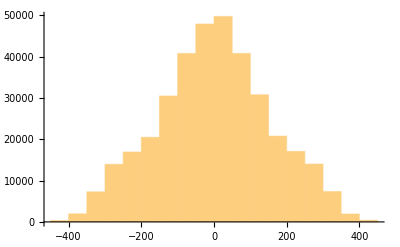

```mathematica
Histogram[ds3]
```